# Network Map Animation Routines

## Functions

```mathematica
<<PajaroLocoPublic`
ImportAndReshapeMosquitoDatasets[dataPath_,{maleFilenamePattern_,femaleFilenamePattern_}]:=Module[{names,dataSets,maleFilenames,femaleFilenames,maleDatasets,femaleDatasets,genotypes,ticksMax,maleMax,femaleMax},
maleFilenames=FileNames[maleFilenamePattern<>"_*.csv",dataPath]//Sort;
femaleFilenames=FileNames[femaleFilenamePattern<>"_Aggregate*.csv",dataPath]//Sort;
maleDatasets=AddTotalPopulationToDataset[Map[Import[#][[2;;All,2;;All]]&,maleFilenames]];
femaleDatasets=AddTotalPopulationToDataset[Map[Import[#][[2;;All,2;;All]]&,maleFilenames]];
genotypes=Import[maleFilenames[[1]]][[1,2;;All]];
ticksMax=Length[maleDatasets[[1]]];
{maleMax,femaleMax}={Flatten[maleDatasets]//Max,Flatten[femaleDatasets]//Max};
(*Output*)
{
{maleDatasets,femaleDatasets},
{genotypes,ticksMax,{maleMax,femaleMax}}
}
]
GenerateColorPalette[genotypes_,colorScheme_]:=Module[{steps,colors},
steps=(genotypes//Length)-1;
colors={ColorData[colorScheme,#]&/@Range[0,1,1/steps],Black}//Flatten;
{Append[genotypes,"Total"],colors}
]
ImportGeoCoordinatesAndKernel[coordinatesFilePath_,kernelFilePath_]:=Module[{cities,transitionsMatrix},
cities={#[[1]],{#[[2]],#[[3]]},#[[4]]}&/@Import[coordinatesFilePath];
transitionsMatrix=Import[kernelFilePath][[2;;All]];
{cities,transitionsMatrix}
]
AddTotalPopulationToDataset[dataset_]:=Table[Append[#,Total[#]]&/@dataset[[i]],{i,1,Length[dataset]}]
AggregatePopulationByGenotypeIndices[populationDatasets_,genotypesIndicesToAggregate_]:=Module[{popsDatasets,geneLabels},
popsDatasets=Table[Transpose[Total/@populationDatasets[[i,All,#[[2]]]]&/@genotypesIndicesToAggregate],{i,1,Length[populationDatasets]}];
geneLabels=genotypesIndicesToAggregate[[All,1]];
{geneLabels,AddTotalPopulationToDataset[popsDatasets]}
]
AggregatePopulationAcrossNodes[aggregatedPopulations_]:=Table[Total/@(aggregatedPopulations[[All,i]]//Transpose),{i,1,Length[aggregatedPopulations[[1]]]}]
SubsetPopulations[{aggregatedPopulations_,aggregatedPopulationsAcrossNodes_},dataRange_]:={aggregatedPopulations[[All,dataRange[[1]];;dataRange[[2]]]]//Transpose,aggregatedPopulationsAcrossNodes[[dataRange[[1]];;dataRange[[2]]]]}
GeneratePopCountsFrames[{labels_,colors_},subsetPopulationsAccrossNodes_]:=Module[{styledLabels,styledNumbers,gridFrames},
styledLabels=Style[#,30]&/@labels;
styledNumbers=Table[Style[Round[#],30,Black]&/@Threshold[i,{"Hard",10^-1}],{i,subsetPopulationsAccrossNodes}];
gridFrames=Table[
Grid[{styledLabels,styledNumbers[[i]]}//Transpose,
Frame->True,
FrameStyle->Thick,
ItemSize->15,
Background->{None,Opacity[.25,#]&/@colors},
Alignment->Center
]
,{i,1,subsetPopulationsAccrossNodes//Length}]
]
BarChartPopCountsFrames[subsetPopulations_,{colors_,maxPop_,frameDimensions_}]:=BarChart[subsetPopulations[[All,1;;(Length[labels]-1)]],
ChartLayout->"Stacked",
ChartStyle->{EdgeForm[None],(Directive[Opacity[1],#]&/@colors )},
Frame->False,
PlotRange->{{.5,Length[subsetPopulations]+.5},{0,maxPop}},
Axes->False,
PerformanceGoal->"Speed",
BarSpacing->.2,
ImagePadding->0,
AspectRatio->1/10,
BarOrigin->Top,
PlotRangePadding->{0,0},
ImageSize->frameDimensions[[1]]
]
BarChartPopDynamicsFrames[tick_,aggregatedPopulationsAcrossNodes_,{colors_,maxPop_,ticksMax_,frameDimensions_,labels_}]:=Module[{dataUntilTick},
dataUntilTick=aggregatedPopulationsAcrossNodes[[1;;tick]][[All,1;;(Length[labels]-1)]];
BarChart[dataUntilTick,
ChartLayout->"Stacked",
ChartStyle->{EdgeForm[None],(Directive[Opacity[1],#]&/@colors )},
Frame->False,
PlotRange->{{0,ticksMax},{0,maxPop}},
Axes->False,
PerformanceGoal->"Speed",
BarSpacing->{0,0},
ImagePadding->0,
AspectRatio->1/10,
BarOrigin->Bottom,
PlotRangePadding->{0,0},
ImageSize->frameDimensions[[1]]
]
]
ExportFrames[plots_,dataRange_,{outputBasePath_,outputFolder_,filesBaseName_}]:=Module[{namesStrings,pathsStrings},
namesStrings=(filesBaseName<>StringPadLeft[ToString[#],6,"0"]<>".png")&/@Range[dataRange[[1]],dataRange[[2]]];
pathsStrings=(outputBasePath<>outputFolder<>#)&/@namesStrings;
Export[#[[1]],#[[2]]]&/@Transpose[{pathsStrings,plots}]
]
BarChartPopDynamicsMaskFrames[fullRaster_,{tick_,ticksMax_}]:=Module[{rasterDimensions,stepSize,composedImage,day=tick},
rasterDimensions=ImageDimensions[fullRaster];
stepSize=rasterDimensions[[1]]/ticksMax//N;
composedImage=ImageCompose[
fullRaster,
Graphics[{
White,Opacity[1],Rectangle[{day*stepSize,0},{day*stepSize+1*stepSize,rasterDimensions[[2]]}],
White,Opacity[.75],Rectangle[{day*stepSize+1*stepSize*stepSize,0},{rasterDimensions[[1]],rasterDimensions[[2]]}],
Black,Opacity[0],Rectangle[{0,0},{rasterDimensions[[1]],rasterDimensions[[2]]}]
},
ImageSize->rasterDimensions[[1]],
AspectRatio->1/5,
ImagePadding->None,
ImageMargins->0,
PlotRangePadding->None
]
]
]
EdgesStyleList2[vertexSyllableList_,OptionsPattern[]]:=Switch[OptionValue[VariableStyle],
"LineColor",Table[DirectedEdge[vertexSyllableList[[i]][[1]][[1]],vertexSyllableList[[i]][[1]][[2]]]->{Opacity[1*vertexSyllableList[[i]][[2]]+.01],Thickness[OptionValue[LineThickness]]},{i,1,Length[vertexSyllableList]}],
"LineWidth",Table[DirectedEdge[vertexSyllableList[[i]][[1]][[1]],vertexSyllableList[[i]][[1]][[2]]]->{Opacity[.5],Blue,Thickness[vertexSyllableList[[i]][[2]]*OptionValue[LineThickness]]},{i,1,Length[vertexSyllableList]}],
"Both",Table[DirectedEdge[vertexSyllableList[[i]][[1]][[1]],vertexSyllableList[[i]][[1]][[2]]]->{Opacity[.75*vertexSyllableList[[i]][[2]]+.05],Thickness[vertexSyllableList[[i]][[2]]*OptionValue[LineThickness]]},{i,1,Length[vertexSyllableList]}],_,Table[DirectedEdge[vertexSyllableList[[i]][[1]][[1]],vertexSyllableList[[i]][[1]][[2]]]->{Thickness[OptionValue[LineThickness]]},{i,1,Length[vertexSyllableList]}]]
edgeshape[e_,___]:={Arrowheads[{{.0001,.5}}],Arrow[e]}
Options[GraphTransitionsFrequenciesWithMax]:={ImagePadding->None,Background->White,VertexStyle->Automatic,VertexCoordinates->Automatic,LineThickness->.0005,VariableStyle->"Both",GraphLayout->Automatic,ImageSize->Automatic,VertexSize->.5,EdgeShapeFunction->edgeshape,VertexLabelStyle->{Italic},Prolog->{},Epilog->{},VertexShape->Automatic}
GraphTransitionsFrequenciesWithMax[frequenciesOutput_,max_,OptionsPattern[]]:=Module[{frequencies,syllables,edges,fixedEdgesList,vertexSyllableList,normalizedVertexSyllableList,edgesStyleList,links},frequencies=frequenciesOutput[[1]];
syllables=frequenciesOutput[[2]];
edges=Table[DirectedEdge[i,j]->frequencies[[i,j]],{i,Length[syllables]},{j,Length[syllables]}]//Flatten;
fixedEdgesList=DeleteCases[edges,DirectedEdge[_,_]->0];
vertexSyllableList=VertexNumberToVertexSyllable[frequenciesOutput[[2]],fixedEdgesList];
normalizedVertexSyllableList=(DirectedEdge[#[[1]],#[[2]][[1]]]->#[[2]][[2]]/max&)/@vertexSyllableList;
edgesStyleList=EdgesStyleList2[normalizedVertexSyllableList,LineThickness->OptionValue[LineThickness],VariableStyle->OptionValue[VariableStyle]];
links=DirectedEdge[#[[1]],#[[2,1]]]&/@vertexSyllableList;
Graph[syllables,links,
AspectRatio->Automatic,
EdgeWeight->vertexSyllableList[[All,2,2]],
VertexStyle->OptionValue[VertexStyle],
EdgeStyle->edgesStyleList,
VertexCoordinates->OptionValue[VertexCoordinates],
ImageSize->OptionValue[ImageSize],
GraphLayout->OptionValue[GraphLayout],
EdgeShapeFunction->OptionValue[EdgeShapeFunction],
VertexShape->OptionValue[VertexShape],
VertexSize->OptionValue[VertexSize],
VertexLabelStyle->OptionValue[VertexLabelStyle],
VertexLabels->Placed["Name",Center],
EdgeLabels->Table[links[[i]]->Placed[fixedEdgesList[[All,2]][[i]],Tooltip],{i,Length[links]}],
Prolog->OptionValue[Prolog],
Epilog->OptionValue[Epilog],
Background->OptionValue[Background],
ImagePadding->OptionValue[ImagePadding],
PerformanceGoal->"Speed"
]
]
CalculateNetworkParameters[cities_,transitionsMatrix_]:=Module[{range,transitionsMatrix2,vertexCoordinates,transMatrix},
range=Range[cities//Length];
transitionsMatrix2={transitionsMatrix,ToString/@range};
vertexCoordinates=cities;
transMatrix={ReplacePart[Chop[transitionsMatrix2[[1]]//UpperTriangularize],{i_,i_}->0],transitionsMatrix2[[2]]};
{range,transMatrix,vertexCoordinates}
]
CalculateVertexScalers[{range_,nodeScaler_},scaledSizesPieChartFramesAtFrame_]:=Module[{vertexShapes,vertexSizes},
vertexShapes=Flatten[{ToString[#[[1]]]->#[[2,1]]}&/@Transpose[{range,scaledSizesPieChartFramesAtFrame}]];
vertexSizes=Flatten[{ToString[#[[1]] ]->nodeScaler*#[[2,2]]}&/@Transpose[{range,scaledSizesPieChartFramesAtFrame}]];
{vertexShapes,vertexSizes}
]
GenerateNetworkFrames[vertexShapeAndSizeFrames_,{vertexCoordinates_,networkMatrix_},{edgeThreshold_,lineThickness_,frameDimensions_},countryMap_,colorPalette_]:=Module[{},
GraphTransitionsFrequenciesWithMax[networkMatrix,edgeThreshold,
VertexCoordinates->vertexCoordinates,
LineThickness->lineThickness,
VertexShape->vertexShapeAndSizeFrames[[1]],
VertexSize->vertexShapeAndSizeFrames[[2]],
VariableStyle->"LineColor",
VertexLabelStyle->Directive[Red,Italic,Opacity[0]],
ImageSize->frameDimensions[[1]],
Prolog->
{
EdgeForm[Directive[Opacity[1],Thickness[.05],Darker[colorPalette[[5]],.06]]],Opacity[.5],colorPalette[[1]],
countryMap[[2]],
EdgeForm[Directive[Opacity[1],Thickness[.05],colorPalette[[5]]]],Opacity[.2],colorPalette[[3]],
countryMap[[2]],
EdgeForm[Directive[Opacity[.25],Thickness[.020],colorPalette[[2]]]],Opacity[0],colorPalette[[5]],
countryMap[[1]]
},
ImagePadding->500
]
]
ParseFilenames[tick_,{outputFolder_,{outputPopCounts_,outputBarCharts_,outputFlow_,outputNetworks_},{baseCounts_,baseDays_,baseBarCharts_,basePopDyn_,baseNetworks_}}]:=Module[{paddedNumber,rastersFolders,rastersNames},
paddedNumber=StringPadLeft[ToString[tick],6,"0"];
rastersFolders=(outputFolder<>#)&/@{outputPopCounts,outputBarCharts,outputFlow,outputNetworks};
rastersNames=(#<>paddedNumber<>".png")&/@{baseCounts,baseDays,baseBarCharts,basePopDyn,baseNetworks};
{
rastersFolders[[1]]<>rastersNames[[1]],
rastersFolders[[1]]<>rastersNames[[2]],
rastersFolders[[2]]<>rastersNames[[3]],
rastersFolders[[3]]<>rastersNames[[4]],
rastersFolders[[4]]<>rastersNames[[5]]
}
]

GeneratePieChartsAtTick[subsetPopulation_,labels_,maxPop_]:=Module[{chartAndPop},
chartAndPop={
PieChart[#,ChartStyle->colors,BaseStyle->Directive[EdgeForm[Directive[Black,Thickness[.15]]]],ColorFunction->(EdgeForm[Black]&),PerformanceGoal->"Speed",ImagePadding->2.25],
Total[#]
}&/@(subsetPopulation[[All,1;;(Length[labels]-1)]]);
{#[[1]],Sqrt[#[[2]]/maxPop]}&/@chartAndPop
]
```

```mathematica
ImportGeoCoordinatesAndKernel[coordinatesFilePath_,kernelFilePath_]:=Module[{cities,transitionsMatrix},
cities={1,{#[[1]],#[[2]]},50}&/@Import[coordinatesFilePath];
transitionsMatrix=Import[kernelFilePath][[1;;All]];
{cities,transitionsMatrix}
]
```

```mathematica
rgbColors={
ColorData[{"LakeColors",{1,0}}][1],
ColorData[{"LakeColors",{1,0}}][0]
};
GenerateBlendSetting[color_]:=Module[{levels},
levels=Level[color,1];
{
RGBColor[levels[[1]],levels[[2]],levels[[3]],0],
RGBColor[levels[[1]],levels[[2]],levels[[3]],1]
}
]
GenerateBlendSettingCMYK[color_]:=Module[{levels},
levels=Level[color,1];
{
RGBColor[levels[[1]],levels[[2]],levels[[3]],0],
RGBColor[levels[[1]],levels[[2]],levels[[3]],1]
}
]
hexifyColor[color_RGBColor]:=StringJoin["#",IntegerString[Round[Level[color,1]*255],16,2]]
hexToRGB=RGBColor@@(IntegerDigits[ToExpression@StringReplace[#,"#"->"16^^"],256,3]/255.)&;
Sigmoid[x_]:=.5+1/(1+ⅇ^(-5x+1.75))
```

```mathematica
GenerateAnimationFrameFromFiles[fileNameTuple_]:=Module[{popCount,dayCount,barChart,flow,network,row},
{popCount,dayCount,barChart,flow,network}=Import[#]&/@fileNameTuple;
row=Grid[{{
ImageRotate[barChart,90Degree]//Show[#,ImageSize->{ImageDimensions[barChart][[2]],ImageDimensions[barChart][[1]]/1.75}]&,
(*dayCount//ImageRotate[Show[#],90Degree]&,*)
network//Show[#,ImageSize->(ImageDimensions[#])]&,
(*popCount//Show[#]&*),
ImageRotate[flow,90Degree]//Show[#,ImageSize->{ImageDimensions[barChart][[2]],ImageDimensions[barChart][[1]]/1.75}]&
}}];
Rasterize[row]
]
```

## Load Data

```mathematica
(*Set the path for the experiments*)
USER=1;
return=If[USER==1,SetDirectory["/Users/sanchez.hmsc/Desktop/SplitDrive/"],1];
(*Subset datasets to export a specific set of frames*)
framesRange={1,2000};
(*User-Defined data range for frames, and aesthetic parameters*)
genotypesIndicesToAggregate={
{"H*",{5,6,7,12,15,16,17,22,25,26,27}},
{"Other",{1,2,3,4,8,9,10,11,13,14,18,19,20,21,23,24,28,29,30}}
};
{frameDimensions,scaler,resolution,colorScheme,nodeScaler}={{2560,1440},3.5,500,"LakeColors",1.5};
(*Import data and calculate necessary values*)
{{maleDatasets,femaleDatasets},{genotypes,ticksMax,{maleMax,femaleMax}}}=ImportAndReshapeMosquitoDatasets["./E_01_01_00020/",{"ADM_Mean","AF1_Mean"}];
```

```mathematica
{outputFolder,outputBarCharts,outputFlow,outputNetworks,outputPopCounts,outputFullFrames}={"./Frames","/BarCharts/","/Flow/","/Networks/","/PopCounts/","/FullFrames/"};
{baseCounts,baseDays,baseBarCharts,basePopDyn,baseNetworks,baseFullFrames}={"PopCount","DayCount","BarCharts","Flow","Networks","FullFrame"};
{Range[Length[genotypes]],genotypes}//Transpose
(*Aggregate dataset*)
totalPopulationDatasets=(maleDatasets+femaleDatasets);
{aggregatedLabels,aggregatedPopulations}=AggregatePopulationByGenotypeIndices[totalPopulationDatasets,genotypesIndicesToAggregate];
aggregatedPopulationsAcrossNodes=AggregatePopulationAcrossNodes[aggregatedPopulations];
{labels,colors}=GenerateColorPalette[aggregatedLabels,colorScheme];
maxPop=aggregatedPopulationsAcrossNodes[[All,Length[labels]]]//Max;
```

{{1,WWWW},{2,WWWH},{3,WWWR},{4,WWWB},{5,WWHH},{6,WWHR},{7,WWHB},{8,WWRR},{9,WWRB},{10,WWBB},{11,WCWW},{12,WCWH},{13,WCWR},{14,WCWB},{15,WCHH},{16,WCHR},{17,WCHB},{18,WCRR},{19,WCRB},{20,WCBB},{21,CCWW},{22,CCWH},{23,CCWR},{24,CCWB},{25,CCHH},{26,CCHR},{27,CCHB},{28,CCRR},{29,CCRB},{30,CCBB}}

```mathematica
originalColorsValues={
{0,90,50,0},
{0,0,0,0}
};
cmykColors=CMYKColor[#[[1]]/100,#[[2]]/100,#[[3]]/100,#[[4]]/100]&/@originalColorsValues;
colors=rgbColors=ColorConvert[#,"CMYK"->"RGB"]&/@cmykColors;
rgbaColors=GenerateBlendSetting[#]&/@rgbColors;
Transpose[{rgbColors,genotypesIndicesToAggregate}]//Grid;
maxPopSize=aggregatedPopulationsAcrossNodes//Flatten//Max;
SwatchLegend[rgbColors,genotypesIndicesToAggregate[[All,1]]
,LabelStyle->30
,LegendMarkerSize->25
]
rgbaColors=GenerateBlendSetting[#]&/@rgbColors;
Export["./frames/"<>"00_ColorSwatch.png",%%,ImageResolution->500];
```

Generate Blank Transitions Matrix

```mathematica
citiesNumber=maleDatasets//Length;
transitionsMatrix=ConstantArray[0,{citiesNumber,citiesNumber}];
scaledTransitionsMatrix=1*(ⅇ^(1000#)-1)&/@ReplacePart[transitionsMatrix,{i_,i_}->0];
meanTransitions=scaledTransitionsMatrix//Flatten//Mean;
networkMatrix=Chop/@UpperTriangularize[scaledTransitionsMatrix];
networkMatrixThreshold=Table[If[#>meanTransitions/1.25,#,0]&/@i,{i,networkMatrix}];
```

Cluster Cities

```mathematica
rawCities=Import["KM_coordinates.csv"][[2;;All]];
{coords,pops}={rawCities[[All,1;;2]],rawCities[[All,3]]};
```

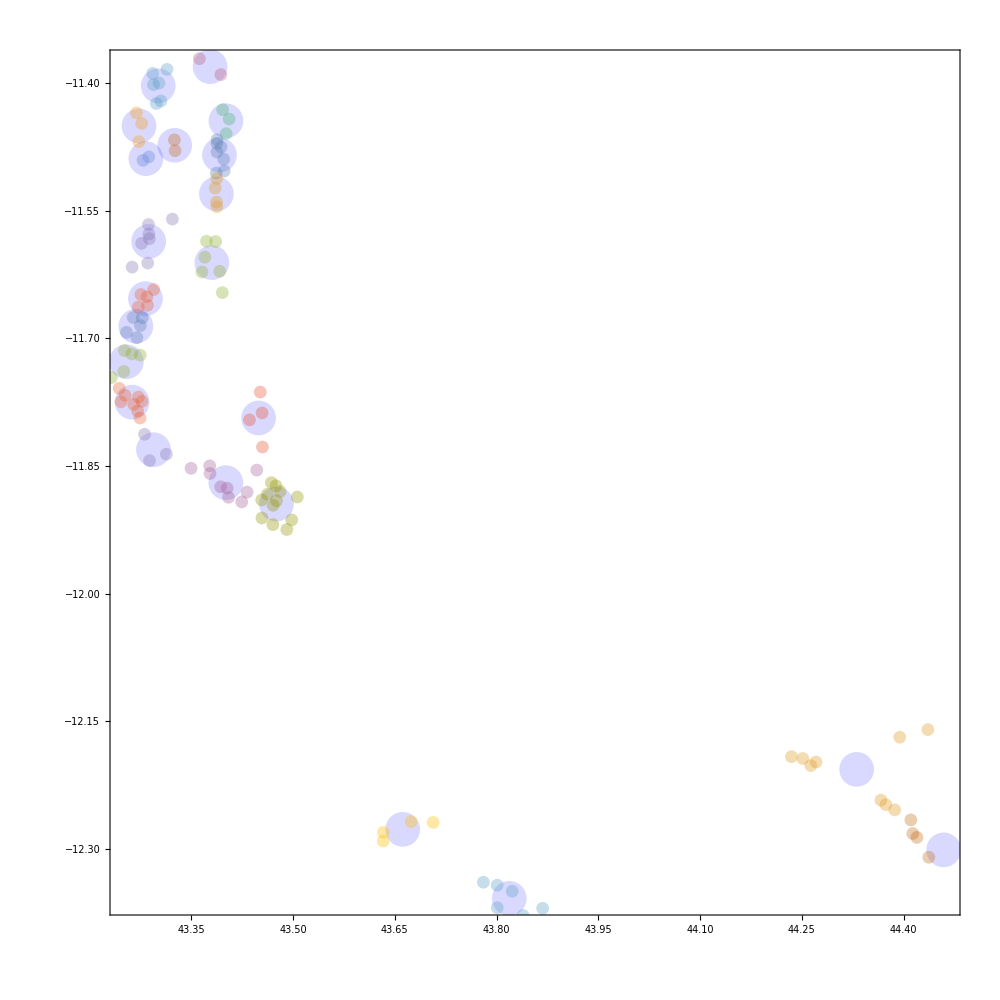

ComorosClusters.pdf

```mathematica
{SEED,CLUSTERS}={42,25};
SeedRandom[SEED]
clustersNumber=CLUSTERS;
clusters=FindClusters[coords ,clustersNumber, Method->"KMeans"];
clustersCentroids={Mean[#[[All,1]]],Mean[#[[All,2]]]}&/@clusters;
clustersIndices=Table[Flatten[Position[coords,#]&/@i],{i,clusters}];
clusteredPopulations=Table[Total[pops[[#]]&/@i],{i,clustersIndices}];
(**)
original=ListPlot[
clusters
,PlotStyle->Directive[Opacity[.35]]
];
clustersRender=ListPlot[clustersCentroids
,AspectRatio->1
,Frame->True
,FrameStyle->Thick
,PlotStyle->Directive[PointSize[.025],Blue,Opacity[.15]]
];
Show[{clustersRender,original},ImageSize->1000]
Export["ComorosClusters.pdf",%]
```

Process Coordinates

```mathematica
{xOffset,yOffset}={0,-.075};
latLongs=clustersCentroids;
populations=clusteredPopulations;
(**)
ordering=Range[latLongs//Length];(*(Reverse/@latLongs)//Ordering//Reverse*)
latLongs={latLongs[[ordering]][[All,1]]+xOffset,latLongs[[ordering]][[All,2]]+yOffset}//Transpose;
populations=populations[[ordering]]
(**)
sizes=Rescale[#,{Log[populations]//Min,Log[populations]//Max},{.05,2}]&/@Log[populations];
minMaxes={Min[#],Max[#]}&/@(latLongs//Transpose);
center=Mean/@minMaxes;
gridSize=Max[Abs[(#[[1]]-#[[2]])]&/@minMaxes]*.6;
```

{1922194,411,1205826,351124,67977,352,3529,5838,3901,1880,6679,84,36,1401,4236,61997,31016,152070,19231,43936,0,6}

Generate Map

{CMYKColor[Rational[7, 10], Rational[1, 2], 0, 0],CMYKColor[0, Rational[9, 10], Rational[1, 2], 0],CMYKColor[0, 0, 0, 0],CMYKColor[1, 1, 1, 1],CMYKColor[0, 0, 0, 0]}

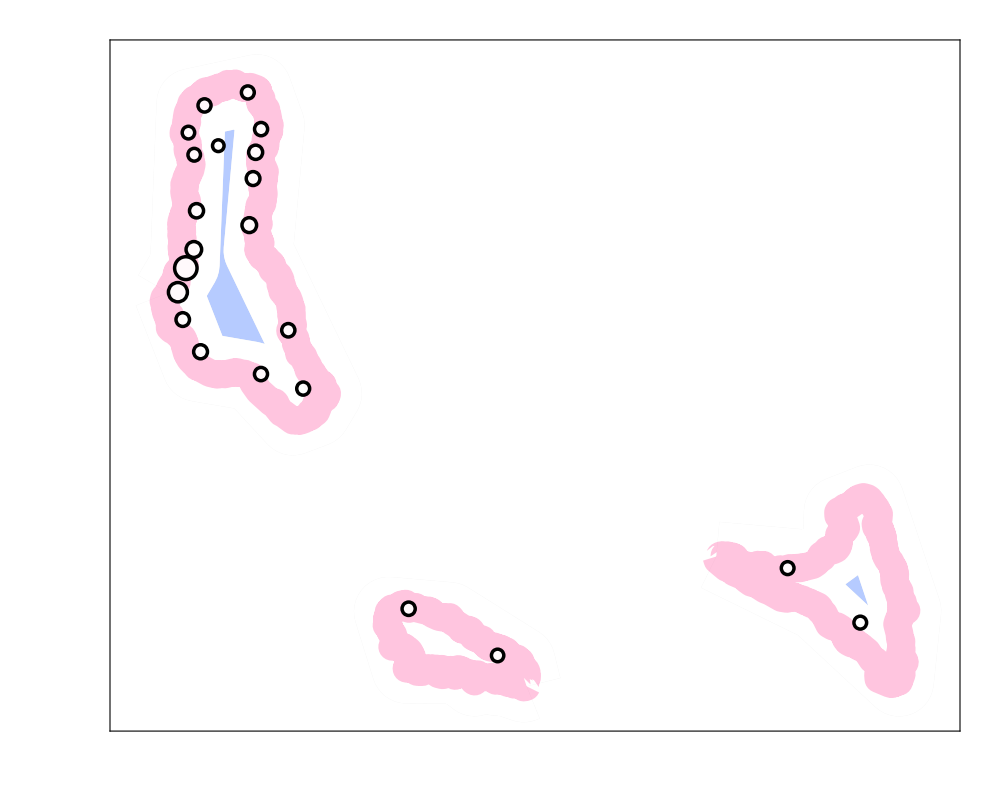

Comoros.pdf

```mathematica
countryName="Comoros";
originalColorsValuesMap={
{70,50,0,0},
{0,90,50,0},
{0,0,0,0},
{100,100,100,100},
{0,0,0,0}
};
(**)
mapPolygons={countryPolygon,countrySchematicPolygon}={CountryData[countryName,"Polygon"],CountryData[countryName,"SchematicPolygon"]};
colorPaletteMap=CMYKColor[#[[1]]/100,#[[2]]/100,#[[3]]/100,#[[4]]/100]&/@originalColorsValuesMap
mapRender=GeoGraphics[{
GeoStyling[EdgeForm[Directive[Opacity[1],Thickness[.05],Darker[colorPaletteMap[[5]],.06]]],Opacity[.5],colorPaletteMap[[1]]],
mapPolygons[[2]],
GeoStyling[EdgeForm[Directive[Opacity[1],Thickness[.05],colorPaletteMap[[5]]]],Opacity[.2],colorPaletteMap[[3]]],
mapPolygons[[2]],
GeoStyling[EdgeForm[Directive[Opacity[.25],Thickness[.020],colorPaletteMap[[2]]]],Opacity[0],colorPaletteMap[[5]]],
mapPolygons[[1]]
}
,AspectRatio->Automatic
,Axes->False
,Frame->True
,FrameStyle->Directive[colorPaletteMap[[4]],Thickness[.0035]]
,FrameTicks->None
,FrameTicksStyle->White
,GridLines->Automatic
,GridLinesStyle->Directive[{Dashing[.0025],Thickness[.00075],colorPaletteMap[[4]]}]
,ImageSize->1000
(*,PlotRange->({#-gridSize,#+gridSize}&/@center)*)
,GeoBackground->None
,Prolog->{colorPaletteMap[[1]],Opacity[.00005],EdgeForm[Directive[Opacity[.00000005],Thickness[.0025],colorPaletteMap[[1]]]]}
,Epilog->{
White,
Opacity[.9],
EdgeForm[Directive[Thickness[.0025],Opacity[1],Black]],
DeleteCases[Disk[#[[1]],Log[1+0.01+#[[2]]/200]]&/@Transpose[{latLongs,sizes//N}],Disk[Missing["NotAvailable"],_]],
Black,
Opacity[0],
Text[
Style[countryName,100,Lighter[colorPaletteMap[[4]],.25],FontFamily->"Zapfino"
],{center[[1]]+.25gridSize,center[[2]]+gridSize*.25}]
}
]
Export["Comoros.pdf",mapRender]
```

Aggregate Counts With GeoClusters

```mathematica
clusteredAggregatedPopulations=Table[Total[aggregatedPopulations[[#]]&/@i],{i,clustersIndices}];
clusteredAggregatedPopulationsAcrossNodes=AggregatePopulationAcrossNodes[clusteredAggregatedPopulations];
```

## Generate Rasters

Flow Chart (only needs to be run once)

```mathematica
barChartPopDynFrames=Map[
BarChartPopDynamicsFrames[#,aggregatedPopulationsAcrossNodes,{colors,maxPopSize,framesRange[[2]],frameDimensions,labels}]&,
{framesRange[[2]]}
];
Export[outputFolder<>"/Flow/"<>"FlowFull.png",barChartPopDynFrames,ImageResolution->300,ImageSize->frameDimensions[[1]]]
```

./Frames/Flow/FlowFull.png

Population Counts

```mathematica
stepSize=8;
Table[
(*Subset Data*)
dataRange={i,i+stepSize};
{subsetPopulations,subsetPopulationsAccrossNodes}=SubsetPopulations[{aggregatedPopulations,aggregatedPopulationsAcrossNodes},dataRange];
(*Export Frames*)
popCountsFrames=GeneratePopCountsFrames[{labels,colors},subsetPopulationsAccrossNodes];
(*popCountGridFrames=Grid[{{#[[1]]},{},{},{#[[2]]}}]&/@Transpose[{dayCounter,popCountsFrames}];*)
ExportFrames[popCountsFrames,dataRange,{outputFolder,outputPopCounts,baseCounts}];
dayCounterFrames=Style[("Day: "<>StringPadLeft[ToString[#],5,"0"]),50]&/@Range[dataRange[[1]],dataRange[[2]]];
ExportFrames[dayCounterFrames,dataRange,{outputFolder,outputPopCounts,baseDays}];
(*Clear Memory*)
ClearSystemCache[];
Clear[dataRange,subsetPopulations,subsetPopulationsAccrossNodes,dayCounterFrames,popCountsFrames];
,{i,framesRange[[1]],framesRange[[2]]-stepSize,stepSize}];
```

$Aborted

Bar Charts

```mathematica
stepSize=8;
Table[
(*Subset Data*)
dataRange={i,i+stepSize};
{subsetPopulations,subsetPopulationsAccrossNodes}=SubsetPopulations[{aggregatedPopulations,aggregatedPopulationsAcrossNodes},dataRange];
(*Export Frames*)
barChartFrames=ParallelMap[
BarChartPopCountsFrames[#,{colors,Ceiling[maleMax+femaleMax],frameDimensions}]&,
subsetPopulations
];
ExportFrames[barChartFrames,dataRange,{outputFolder,outputBarCharts,baseBarCharts}];
(*Clear Memory*)
ClearSystemCache[];
Clear[dataRange,subsetPopulations,subsetPopulationsAccrossNodes,days,barChartFrames];
,{i,framesRange[[1]],framesRange[[2]]-stepSize,stepSize}];
```

$Aborted

Population Dynamics

```mathematica
stepSize=8;
Table[
(*Subset Data*)
dataRange={i,i+stepSize};
{subsetPopulations,subsetPopulationsAccrossNodes}=SubsetPopulations[{aggregatedPopulations,aggregatedPopulationsAcrossNodes},dataRange];
(*Export Frames*)
fullRaster=Import[outputFolder<>outputFlow<>"FlowFull.png"];
days=Range[dataRange[[1]],dataRange[[2]]];
barChartPopDynMaskedFrames=ParallelMap[BarChartPopDynamicsMaskFrames[fullRaster,{#,framesRange[[2]]}]&,days];
ExportFrames[barChartPopDynMaskedFrames,dataRange,{outputFolder,outputFlow,basePopDyn}];
(*Clear Memory*)
ClearSystemCache[];
Clear[dataRange,subsetPopulations,subsetPopulationsAccrossNodes,days,barChartPopDynMaskedFrames];
,{i,framesRange[[1]],framesRange[[2]]-stepSize,stepSize}];
```

Map

Part::take: Cannot take positions 2000 through 2004 in {{0,1.70145×10^7,1.70145×10^7},{0,1.70148×10^7,1.70148×10^7},{0,1.70149×10^7,1.70149×10^7},{0,1.70159×10^7,1.70159×10^7},{0,1.70159×10^7,1.70159×10^7},{0,1.70163×10^7,1.70163×10^7},{0,1.70157×10^7,1.70157×10^7},{0,1.70147×10^7,1.70147×10^7},{0,1.70143×10^7,1.70143×10^7},{0,1.70145×10^7,1.70145×10^7},{0,1.70142×10^7,1.70142×10^7},{0,1.70148×10^7,1.70148×10^7},{0,1.70158×10^7,1.70158×10^7},{0,1.70153×10^7,1.70153×10^7},{0,1.70158×10^7,1.70158×10^7},{0,1.70167×10^7,1.70167×10^7},{0,1.70171×10^7,1.70171×10^7},{0,1.70175×10^7,1.70175×10^7},{0,1.70166×10^7,1.70166×10^7},{3.28236×10^7,1.70156×10^7,4.98392×10^7},{2.56864×10^7,1.70149×10^7,4.27013×10^7},{2.01029×10^7,1.70138×10^7,3.71167×10^7}}.

{{{{0,8.41452×10^6,8.41452×10^6},{0,1920.,1920.},{0,5.28244×10^6,5.28244×10^6},{0,1.54332×10^6,1.54332×10^6},{0,298034.,298034.},{0,1595.8,1595.8},{0,15531.2,15531.2},{0,25421.8,25421.8},{0,17134.8,17134.8},{0,8422.4,8422.4},{0,29388.8,29388.8},{0,399.,399.},{0,189.4,189.4},{0,6141.2,6141.2},{0,18549.,18549.},{0,271409.,271409.},{0,135854.,135854.},{0,666136.,666136.},{0,84338.2,84338.2},{0,192263.,192263.},{0,39.8,39.8},{0,144.4,144.4}},{{0,8.41431×10^6,8.41431×10^6},{0,1920.,1920.},{0,5.28171×10^6,5.28171×10^6},{0,1.54305×10^6,1.54305×10^6},{0,297986.,297986.},{0,1593.2,1593.2},{0,15527.,15527.},{0,25439.6,25439.6},{0,17125.,17125.},{0,8372.4,8372.4},{0,29400.6,29400.6},{0,401.,401.},{0,190.8,190.8},{0,6141.6,6141.6},{0,18550.8,18550.8},{0,271511.,271511.},{0,135878.,135878.},{0,665927.,665927.},{0,84407.4,84407.4},{0,192210.,192210.},{0,42.6,42.6},{0,140.8,140.8}},{{0,8.41426×10^6,8.41426×10^6},{0,1913.,1913.},{0,5.28209×10^6,5.28209×10^6},{0,1.54301×10^6,1.54301×10^6},{0,297976.,297976.},{0,1596.6,1596.6},{0,15540.8,15540.8},{0,25461.8,25461.8},{0,17150.8,17150.8},{0,8373.2,8373.2},{0,29422.6,29422.6},{0,402.4,402.4},{0,193.6,193.6},{0,6156.8,6156.8},{0,18503.8,18503.8},{0,271485.,271485.},{0,135870.,135870.},{0,665670.,665670.},{0,84442.6,84442.6},{0,192290.,192290.},{0,42.2,42.2},{0,140.6,140.6}},{{0,8.41452×10^6,8.41452×10^6},{0,1895.2,1895.2},{0,5.28224×10^6,5.28224×10^6},{0,1.54297×10^6,1.54297×10^6},{0,297998.,297998.},{0,1582.8,1582.8},{0,15577.2,15577.2},{0,25486.8,25486.8},{0,17175.4,17175.4},{0,8382.2,8382.2},{0,29362.8,29362.8},{0,395.6,395.6},{0,192.6,192.6},{0,6172.8,6172.8},{0,18497.8,18497.8},{0,271419.,271419.},{0,135983.,135983.},{0,665673.,665673.},{0,84414.8,84414.8},{0,192340.,192340.},{0,42.8,42.8},{0,140.8,140.8}},{{0,8.4143×10^6,8.4143×10^6},{0,1900.,1900.},{0,5.28226×10^6,5.28226×10^6},{0,1.54292×10^6,1.54292×10^6},{0,297815.,297815.},{0,1585.,1585.},{0,15565.,15565.},{0,25532.4,25532.4},{0,17184.2,17184.2},{0,8375.2,8375.2},{0,29370.,29370.},{0,398.,398.},{0,193.8,193.8},{0,6167.6,6167.6},{0,18505.,18505.},{0,271386.,271386.},{0,136020.,136020.},{0,665810.,665810.},{0,84477.4,84477.4},{0,192204.,192204.},{0,41.4,41.4},{0,143.6,143.6}}},{{0,1.70145×10^7,1.70145×10^7},{0,1.70148×10^7,1.70148×10^7},{0,1.70149×10^7,1.70149×10^7},{0,1.70159×10^7,1.70159×10^7},{0,1.70159×10^7,1.70159×10^7},{0,1.70163×10^7,1.70163×10^7},{0,1.70157×10^7,1.70157×10^7},{0,1.70147×10^7,1.70147×10^7},{0,1.70143×10^7,1.70143×10^7},{0,1.70145×10^7,1.70145×10^7},{0,1.70142×10^7,1.70142×10^7},{0,1.70148×10^7,1.70148×10^7},{0,1.70158×10^7,1.70158×10^7},{0,1.70153×10^7,1.70153×10^7},{0,1.70158×10^7,1.70158×10^7},{0,1.70167×10^7,1.70167×10^7},{0,1.70171×10^7,1.70171×10^7},{0,1.70175×10^7,1.70175×10^7},{0,1.70166×10^7,1.70166×10^7},{3.28236×10^7,1.70156×10^7,4.98392×10^7},{2.56864×10^7,1.70149×10^7,4.27013×10^7},{2.01029×10^7,1.70138×10^7,3.71167×10^7}}⟦2000;;2004⟧}

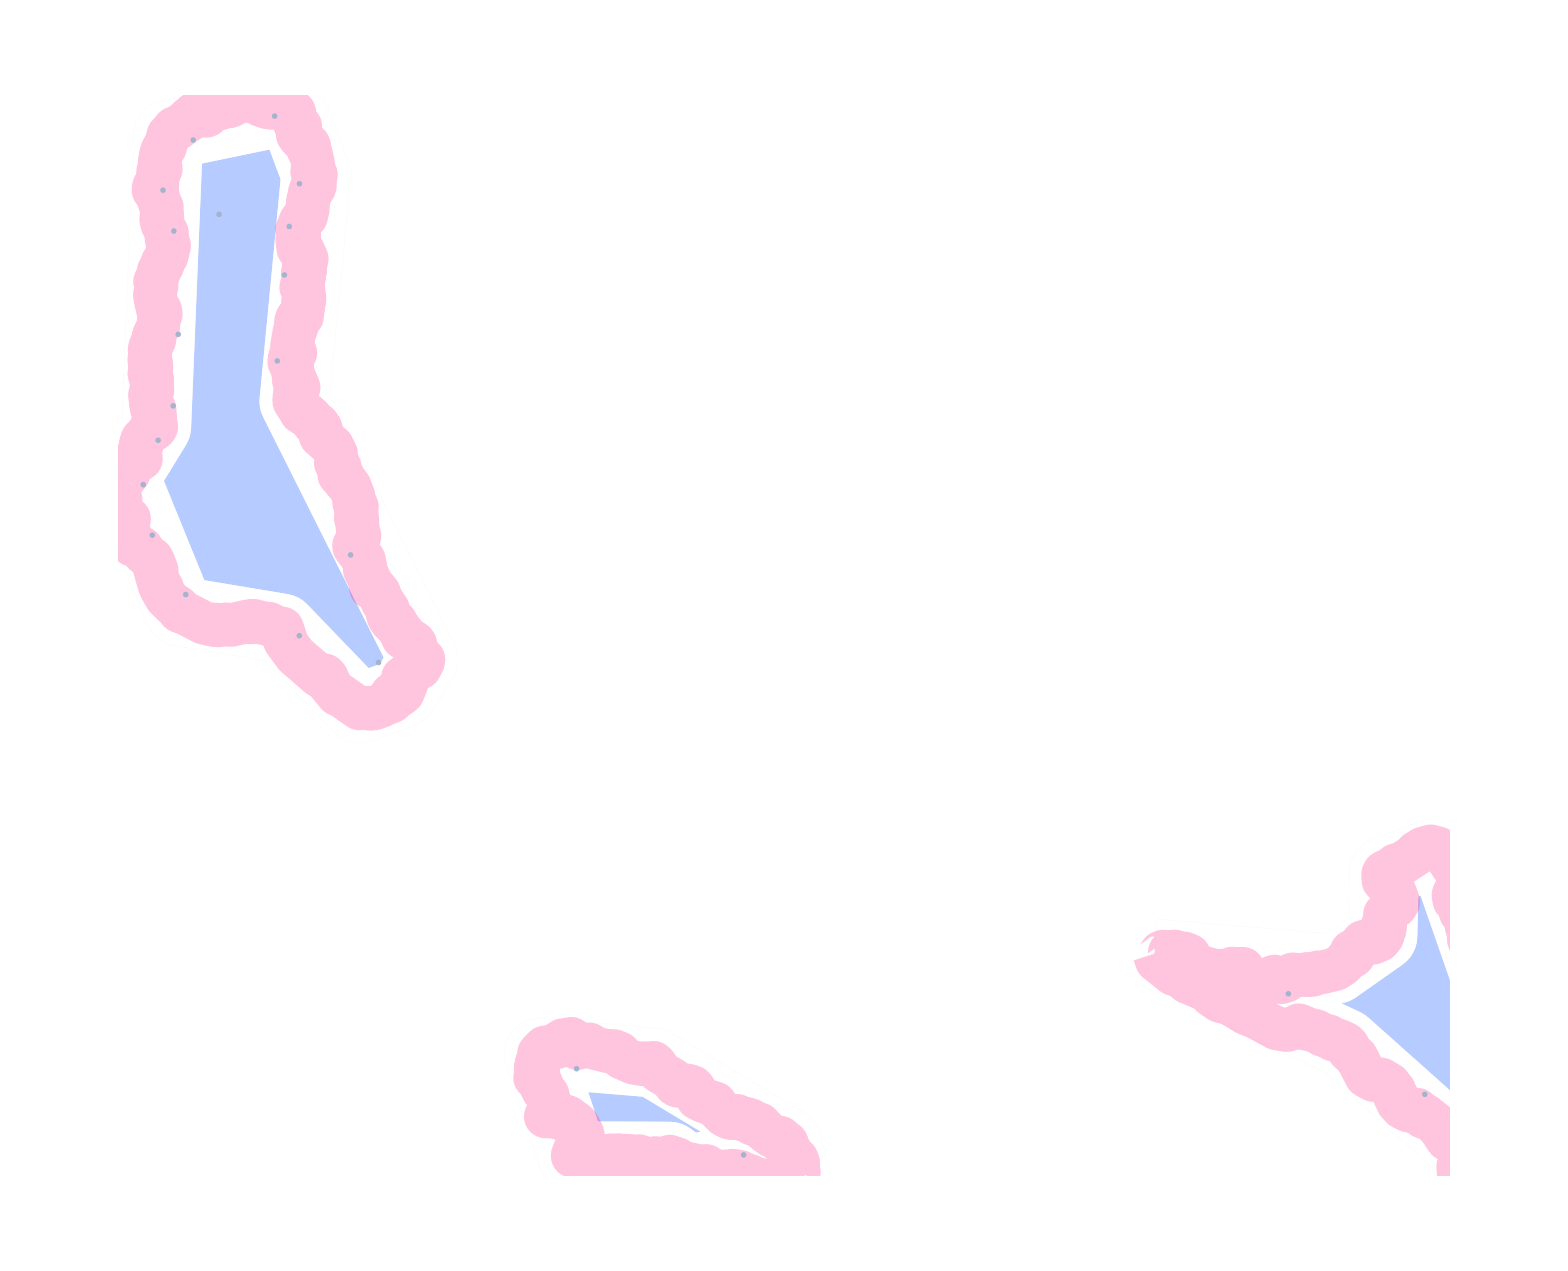
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
i=2000;
stepSize=4;
(*Subset Data*)
dataRange={i,i+stepSize};
subsetPopulations=SubsetPopulations[{clusteredAggregatedPopulations[[ordering]],aggregatedPopulationsAcrossNodes[[ordering]]},dataRange]
pieChartFrames=ParallelMap[GeneratePieChartsAtTick[#,labels,maleMax+femaleMax]&,subsetPopulations[[1]]];
pieChartFrames=(Table[{#[[1]],Sigmoid[#[[2]]]}&/@i,{i,pieChartFrames}]);
{range,networkMatrix,vertexCoordinates}=CalculateNetworkParameters[latLongs,transitionsMatrix];
vertexShapeAndSizeFrames=ParallelMap[CalculateVertexScalers[{range,nodeScaler*.775},#]&,pieChartFrames];
networkFrames=ParallelTable[
GenerateNetworkFrames[vertexShapeAndSizeFrames[[j]],{{#[[1]],#[[2]]+.075}&/@vertexCoordinates,networkMatrix},{1,.0001,frameDimensions},mapPolygons,colorPaletteMap]
,{j,1,stepSize+1}]
```

```mathematica
stepSize=4;
Table[
(*Subset Data*)
dataRange={i,i+stepSize};
subsetPopulations=SubsetPopulations[{clusteredAggregatedPopulations[[ordering]],aggregatedPopulationsAcrossNodes[[ordering]]},dataRange];
pieChartFrames=ParallelMap[GeneratePieChartsAtTick[#,labels,maleMax+femaleMax]&,subsetPopulations[[1]]];
pieChartFrames=Table[{#[[1]],Sigmoid[#[[2]]]}&/@i,{i,pieChartFrames}];
{range,networkMatrix,vertexCoordinates}=CalculateNetworkParameters[latLongs,transitionsMatrix];
vertexShapeAndSizeFrames=ParallelMap[CalculateVertexScalers[{range,nodeScaler*.775},#]&,pieChartFrames];
networkFrames=ParallelTable[
GenerateNetworkFrames[vertexShapeAndSizeFrames[[j]],{{#[[1]],#[[2]]+.075}&/@vertexCoordinates,networkMatrix},{1,.0001,frameDimensions},mapPolygons,colorPaletteMap]
,{j,1,stepSize+1}];
ExportFrames[networkFrames,dataRange,{outputFolder,outputNetworks,baseNetworks}];
(*Clear Memory*)
ClearSystemCache[];
Clear[dataRange,subsetPopulations,pieChartFrames,vertexShapeAndSizeFrames,networkFrames,range,networkMatrix,vertexCoordinates];
,{i,framesRange[[1]],framesRange[[2]]-stepSize,stepSize}];
```

Part::take: Cannot take positions 21 through 25 in {{0,1.70145×10^7,1.70145×10^7},{0,1.70148×10^7,1.70148×10^7},{0,1.70149×10^7,1.70149×10^7},{0,1.70159×10^7,1.70159×10^7},{0,1.70159×10^7,1.70159×10^7},{0,1.70163×10^7,1.70163×10^7},{0,1.70157×10^7,1.70157×10^7},{0,1.70147×10^7,1.70147×10^7},{0,1.70143×10^7,1.70143×10^7},{0,1.70145×10^7,1.70145×10^7},{0,1.70142×10^7,1.70142×10^7},{0,1.70148×10^7,1.70148×10^7},{0,1.70158×10^7,1.70158×10^7},{0,1.70153×10^7,1.70153×10^7},{0,1.70158×10^7,1.70158×10^7},{0,1.70167×10^7,1.70167×10^7},{0,1.70171×10^7,1.70171×10^7},{0,1.70175×10^7,1.70175×10^7},{0,1.70166×10^7,1.70166×10^7},{3.28236×10^7,1.70156×10^7,4.98392×10^7},{2.56864×10^7,1.70149×10^7,4.27013×10^7},{2.01029×10^7,1.70138×10^7,3.71167×10^7}}.

Part::take: Cannot take positions 25 through 29 in {{0,1.70145×10^7,1.70145×10^7},{0,1.70148×10^7,1.70148×10^7},{0,1.70149×10^7,1.70149×10^7},{0,1.70159×10^7,1.70159×10^7},{0,1.70159×10^7,1.70159×10^7},{0,1.70163×10^7,1.70163×10^7},{0,1.70157×10^7,1.70157×10^7},{0,1.70147×10^7,1.70147×10^7},{0,1.70143×10^7,1.70143×10^7},{0,1.70145×10^7,1.70145×10^7},{0,1.70142×10^7,1.70142×10^7},{0,1.70148×10^7,1.70148×10^7},{0,1.70158×10^7,1.70158×10^7},{0,1.70153×10^7,1.70153×10^7},{0,1.70158×10^7,1.70158×10^7},{0,1.70167×10^7,1.70167×10^7},{0,1.70171×10^7,1.70171×10^7},{0,1.70175×10^7,1.70175×10^7},{0,1.70166×10^7,1.70166×10^7},{3.28236×10^7,1.70156×10^7,4.98392×10^7},{2.56864×10^7,1.70149×10^7,4.27013×10^7},{2.01029×10^7,1.70138×10^7,3.71167×10^7}}.

Part::take: Cannot take positions 29 through 33 in {{0,1.70145×10^7,1.70145×10^7},{0,1.70148×10^7,1.70148×10^7},{0,1.70149×10^7,1.70149×10^7},{0,1.70159×10^7,1.70159×10^7},{0,1.70159×10^7,1.70159×10^7},{0,1.70163×10^7,1.70163×10^7},{0,1.70157×10^7,1.70157×10^7},{0,1.70147×10^7,1.70147×10^7},{0,1.70143×10^7,1.70143×10^7},{0,1.70145×10^7,1.70145×10^7},{0,1.70142×10^7,1.70142×10^7},{0,1.70148×10^7,1.70148×10^7},{0,1.70158×10^7,1.70158×10^7},{0,1.70153×10^7,1.70153×10^7},{0,1.70158×10^7,1.70158×10^7},{0,1.70167×10^7,1.70167×10^7},{0,1.70171×10^7,1.70171×10^7},{0,1.70175×10^7,1.70175×10^7},{0,1.70166×10^7,1.70166×10^7},{3.28236×10^7,1.70156×10^7,4.98392×10^7},{2.56864×10^7,1.70149×10^7,4.27013×10^7},{2.01029×10^7,1.70138×10^7,3.71167×10^7}}.

General::stop: Further output of Part::take will be suppressed during this calculation.

$Aborted

## Final Frames

```mathematica
stepSize=4;
Table[
(*Subset Data*)
dataRange={i,i+stepSize};
{subsetPopulations,subsetPopulationsAccrossNodes}=SubsetPopulations[{aggregatedPopulations,aggregatedPopulationsAcrossNodes},dataRange];
(*Export Frames*)
fileNames=ParseFilenames[#,
{
outputFolder,
{outputPopCounts,outputBarCharts,outputFlow,outputNetworks},
{baseCounts,baseDays,baseBarCharts,basePopDyn,baseNetworks}
}]&/@Range[dataRange[[1]],dataRange[[2]]];
fullFrames=ParallelMap[GenerateAnimationFrameFromFiles[#]&,fileNames];
ExportFrames[fullFrames,dataRange,{outputFolder,outputFullFrames,baseFullFrames}];
(*Clear Memory*)
ClearSystemCache[];
Clear[dataRange,subsetPopulations,subsetPopulationsAccrossNodes,fileNames,fullFrames];
,{i,framesRange[[1]],framesRange[[2]]-stepSize,stepSize}];
```